```mathematica
Quit
```

```mathematica
LaunchKernels[];
```

```mathematica
SetDirectory[NotebookDirectory[]];
Get["../lib/lib2.m"];
Get["../lib/util.m"];
```

```mathematica
hasNan[data_] := Module[{}, (
Do[
If[AnyTrue[Head/@data[[Length[data]-i+1]], #===String&], Return[True, Module];Break[];]
, {i, 1, Length[data]}];
Return[False, Module];
)];
```

```mathematica
$K = 3;
```

```mathematica
SymTr[line_] := Module[{t, x}, (
Do[
t = First@line;
x[i] = line[[2+(i-1)(($N)^2-1);; 1+i(($N)^2-1)]];
, {i, 1, $K}];
{t, Table[x[i].x[j] - KroneckerDelta[i, j]/($K)Sum[x[k].x[k], {k, 1, $K}], {i, 1, $K}, {j, 1, $K}]}
)];
```

```mathematica
computeStats[data_] := Module[{rad, symTr, fns}, (
rad = radius/@data;
symTr = SymTr/@data;

fns = {Mean, StandardDeviation};

Join[{#[rad[[All, 2]]]&/@fns},
Flatten[#, 1]&@Table[#[symTr[[All, 2]][[i, j]]]&/@fns, {i, 1, $K-1}, {j, i, $K}]]
)];
```

```mathematica
If[!DirectoryQ["../../runs/Stats-New"], CreateDirectory["../../runs/Stats-New"]];
ParallelDo[Module[{$dirname, $files, $data, $stats, $out, statFile}, (
changeNK[$N, $K];
$dirname = "../../runs/Trials/N"<>ToString@$N<>"K"<>ToString@$K;
$files = FileBaseName/@FileNames[All, $dirname];
Do[(
$data = Import[$dirname<>"/"<>$files[[k]]<>".dat"];

If[hasNan[$data], Print["Detected nan, skipping"];Continue[]];

$stats = computeStats[$data];

$out = Join[{$files[[k]]}, Flatten@$stats];

statFile = OpenAppend["../../runs/Stats-New/N"<>ToString[$N]<>"K"<>ToString[$K]<>".dat"];
WriteString[statFile, StringRiffle[ToString/@$out, "    "]<>"\n"];
Close[statFile];
), {k, 1, Length[$files]}]
)], {$N, 5, 6}]
```

```mathematica
data = Import["../../runs/Trials/N5K9/59555855.dat"];
```

```mathematica
data = data[[1;;10000]];
```

```mathematica
Export["../vals.dat", (radius/@data)[[All, 2]]]
```

../vals.dat

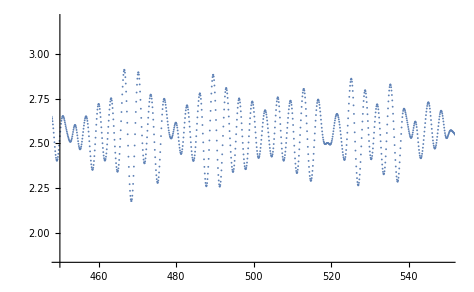

```mathematica
ListPlot[(radius/@data), PlotRange->{{450, 550}, Automatic}]
```

```mathematica
Export["../vals-2.dat",(SymTr/@data)[[All, 2]][[All, 1, 2]]]
```

../vals-2.dat

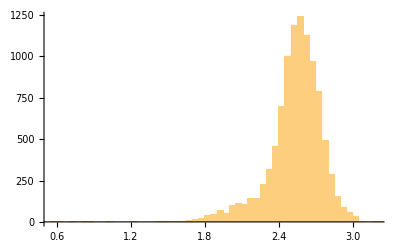

```mathematica
Histogram[(radius/@data)[[All, 2]], 100]
```

```mathematica
ShapiroWilkTest[(radius/@data)[[6000;;, 2]]]
```

0.0000197824

```mathematica
changeNK[5, 9];
```

```mathematica
cdata = cMat[data];
```

```mathematica
EigenvaluesContinuous[cdata_, $tSize_] := Module[{goodlist, eiglist}, (
goodlist = {{cdata[[1, 1]], Eigenvalues@cdata[[1, 2]]}};
eiglist = {Eigenvalues@cdata[[1, 2]]};
Module[{e, sortede, f}, Do[(
e = Eigenvalues[cdata[[t, 2]]];

sortede = Table[(
f = Quiet[Interpolation[eiglist[[All, m]]][Length[eiglist] + 1]];
First@Nearest[e, f]
), {m, 1, Length[e]}];

If[Length[eiglist] >= $tSize, 
eiglist = Append[eiglist[[2;;]], sortede], 
AppendTo[eiglist, sortede]
];

AppendTo[goodlist, {cdata[[t, 1]], sortede}];
), {t, 2, Length[cdata]}]];
goodlist
)];
```

```mathematica
ee = EigenvaluesContinuous[cdata, 50];
```

```mathematica
p  = Thread[{ee[[All, 1]],ee[[All, 2, 1]]}]
```

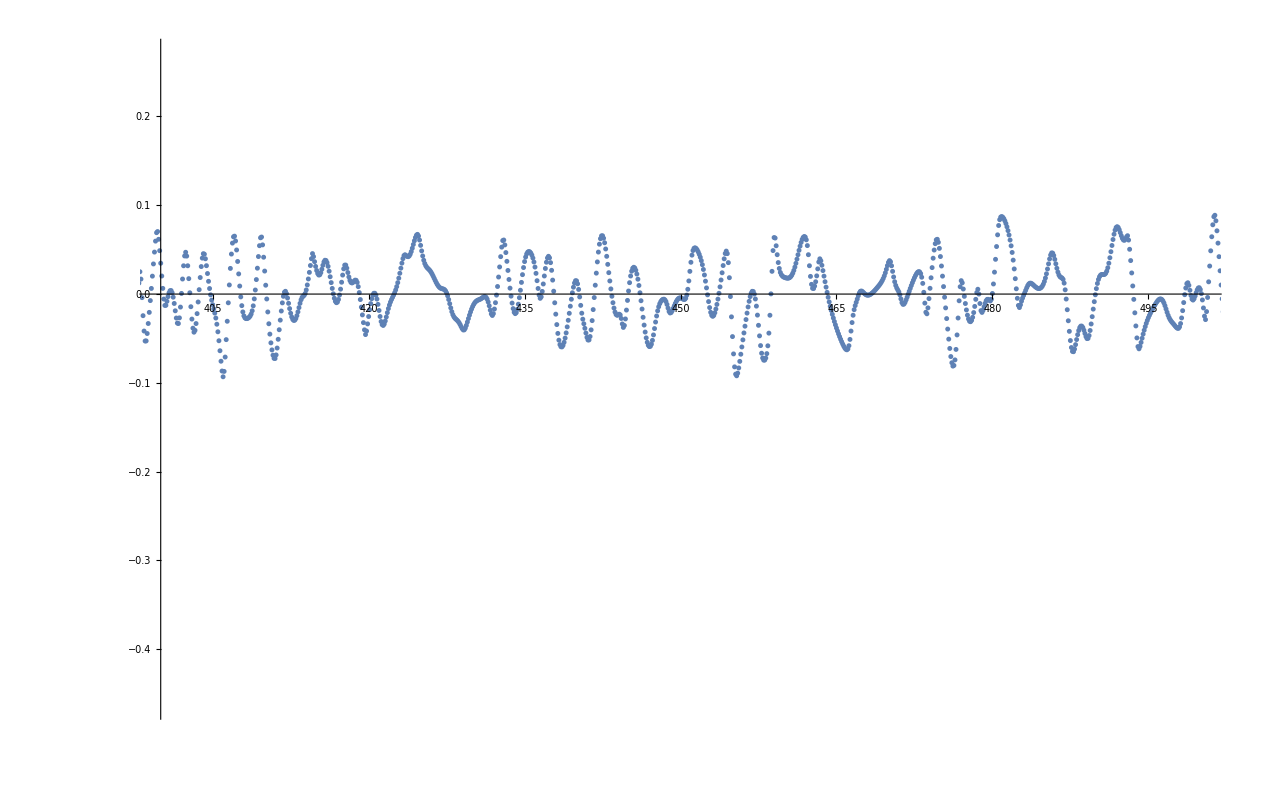

```mathematica
ListPlot[p, PlotRange->{{400, 500}, Automatic}]
```

```mathematica
ee[[5000]]
```

{499.9,{0.00713008,0.254621,-0.121184,-0.121184,0.132288}}

```mathematica
Eigenvectors@cdata[[5000, 2]]
```

{{-0.288722+0.0438287 ⅈ,-0.593943+0.139534 ⅈ,-0.633886-0.146361 ⅈ,0.0689854-0.146309 ⅈ,0.305095+0. ⅈ},{-0.743295-0.0187948 ⅈ,0.35089-0.0229377 ⅈ,0.249498+0.0486016 ⅈ,0.116125-0.3677 ⅈ,0.33198+0. ⅈ},{0.299797+0.173524 ⅈ,-0.0210081-0.500079 ⅈ,-0.0725846+0.465369 ⅈ,0.524436-0.113429 ⅈ,0.346057+0. ⅈ},{0.170772+0.145813 ⅈ,-0.105368+0.331498 ⅈ,0.396212-0.218985 ⅈ,0.0518501+0.396967 ⅈ,0.680714+0. ⅈ},{-0.24852+0.360143 ⅈ,-0.310975+0.189455 ⅈ,0.289999-0.035793 ⅈ,0.598031+0.13905 ⅈ,-0.462146+0. ⅈ}}

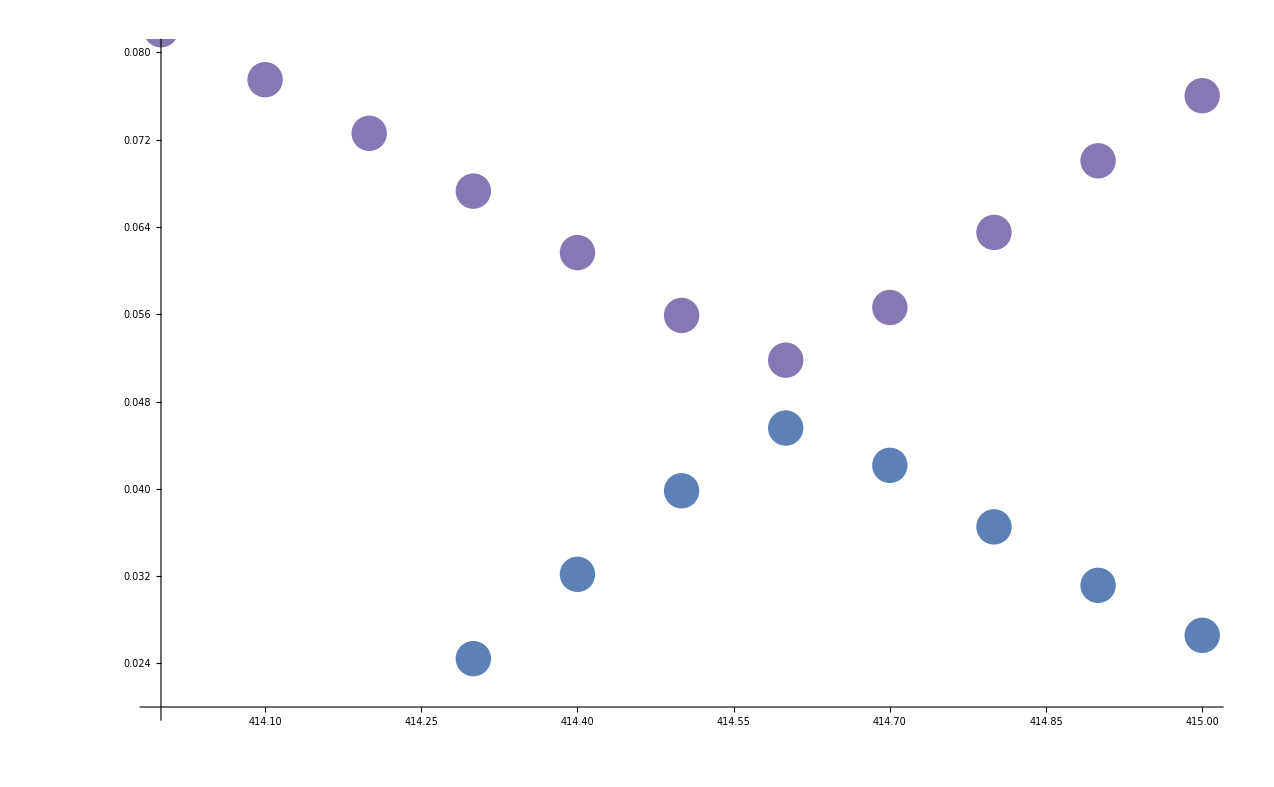

```mathematica
Show[ListPlot[Thread[Table[{#[[1]], y}, {y, #[[2]]}]&/@ee], PlotRange->{{414, 415}, {0.02, 0.08}}, PlotStyle->PointSize[0.02]](*, Plot[Interpolation[p][t], {t, 34, 36},PlotStyle->Purple]*)]
```

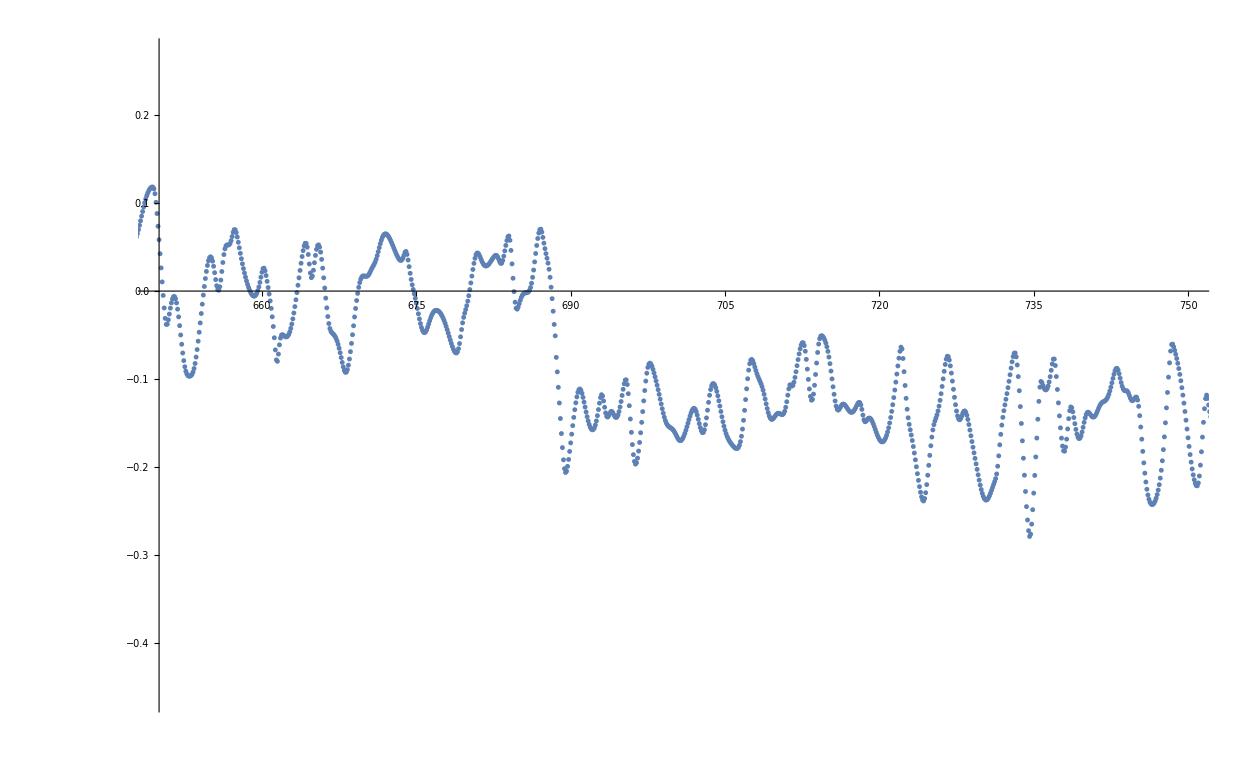

```mathematica
ListPlot[Thread[{ee[[All, 1]],ee[[All, 2, 1]]}], PlotRange->{{650, 750}, Automatic}]
```

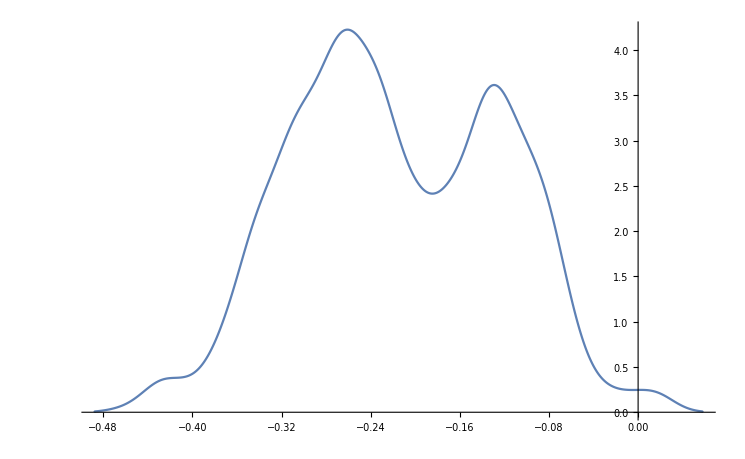

```mathematica
SmoothHistogram[ee[[All, 2, 4]]]
```